```mathematica
t=Log[Abs[x-1]]+c
t-c=Log[Abs[x-1]]
Abs[x-1]=ⅇ^(t-c)
Abs[x-1]=ⅇ^t*ⅇ^-c
```

```mathematica
x-1=A*ⅇ^t
```

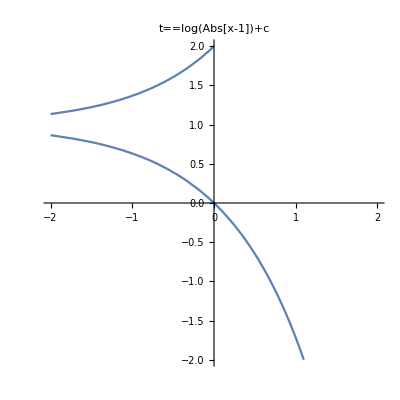

```mathematica
ContourPlot[t==Log[Abs[x-1]],{t,-2,2},{x,-2,2},Axes->True,Frame->False,PlotLabel->t==Log[Abs[x-1]]+c]
```

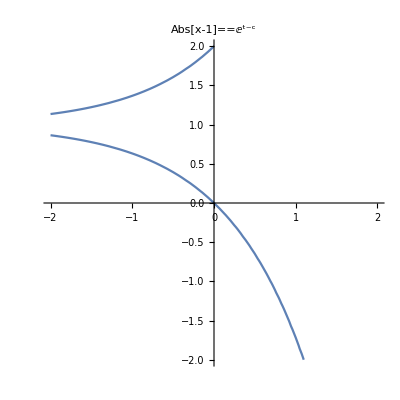

```mathematica
ContourPlot[Abs[x-1]==ⅇ^t,{t,-2,2},{x,-2,2},Axes->True,Frame->False,PlotLabel->Abs[x-1]==ⅇ^(t-c)]
```

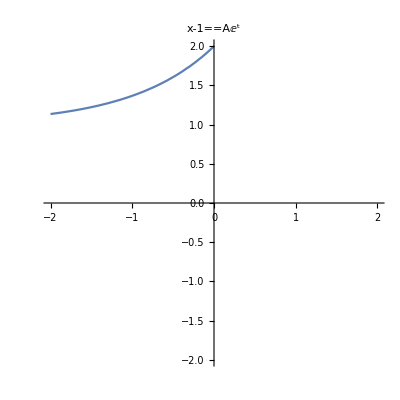
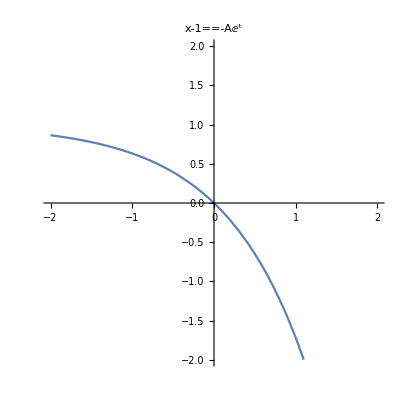

```mathematica
{ContourPlot[x-1==ⅇ^t,{t,-2,2},{x,-2,2},Axes->True,Frame->False,PlotLabel->x-1==Aⅇ^t],ContourPlot[x-1==-ⅇ^t,{t,-2,2},{x,-2,2},Axes->True,Frame->False,PlotLabel->x-1==-Aⅇ^t]}
```